# Correlation matrices

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
attributes = First@Import@First@Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","Curated","Prices_BMV"}]],FileExtension[#]=="csv"&];

datedFiles = Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","Curated","Prices_BMV"}]],FileExtension[#]=="wdx"&];
importedDates = Apply[Join,ProgressMap[Import,datedFiles]];

dates = importedDates[[All,1]];
pricesMatrix = importedDates[[All,2]];
returnsMatrix = Transpose@Map[Returns,Transpose[pricesMatrix]];
```

```mathematica
Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","Curated","Prices_BMV"}]],FileExtension[#]=="wdx"&]
```

{/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/20-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/21-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/22-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/23-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/24-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/27-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/28-01-2020.wdx,/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/Curated/Prices_BMV/29-01-2020.wdx}

```mathematica
window = 1500;
pricesPartitioned = Partition[pricesMatrix,window,1];
returnsPartitioned = Partition[returnsMatrix,window,1];
```

```mathematica
corrMatricesPrices = ProgressTable[UpperTriangularize[Correlation[pricesPartitioned[[i]]],1],{i,1,Length[pricesPartitioned]}];
corrMatricesReturns = ProgressTable[UpperTriangularize[Correlation[returnsPartitioned[[i]]],1],{i,1,Length[returnsPartitioned]}];
```

```mathematica
Manipulate[
Row@{
MatrixPlot[corrMatricesPrices[[i]],PlotLabel->dates[[i+window]],ImageSize->300,PlotRange->{-1,1}],
MatrixPlot[corrMatricesReturns[[i]],PlotLabel->dates[[i+window]],ImageSize->300,PlotRange->{-1,1}]
},
{i,1,Length[corrMatricesReturns],1}
]
```

Denoised

```mathematica
ApplyCorrelationThreshold[corrMatrix_,threshold_]:=ReplaceAll[corrMatrix,{x_ /; (Abs[x]<threshold)->0,x_ /; (Abs[x]≥threshold):>x}];
```

```mathematica
Manipulate[
Row@{
MatrixPlot[ApplyCorrelationThreshold[corrMatricesPrices[[i]],0.5],PlotLabel->dates[[i+window]],ImageSize->300,PlotRange->{-1,1}],
MatrixPlot[ApplyCorrelationThreshold[corrMatricesReturns[[i]],0.5],PlotLabel->dates[[i+window]],ImageSize->300,PlotRange->{-1,1}]
},
{i,1,Length[corrMatricesReturns],1}
]
```

```mathematica
GetGraphFromPositiveCorrelations[corrMatrix_,threshold_,attributes_]:=Block[{zeroedCorrMatrices,adjacencyMatrix},
zeroedCorrMatrices = ReplaceAll[corrMatrix,Indeterminate->0];
adjacencyMatrix = ReplaceAll[
zeroedCorrMatrices*(1-IdentityMatrix[Length[zeroedCorrMatrices]]),
{x_ /; (x<threshold)->0,x_ /; (x≥threshold)->1}
];
AdjacencyGraph[adjacencyMatrix,VertexLabels->Thread[Range[Length[attributes]]->attributes]]
];
```

```mathematica
graphs = ProgressTable[GetGraphFromPositiveCorrelations[corrMatrices[[i]],0.7,attributes],{i,1,Length[corrMatrices]}];
```

```mathematica
Manipulate[Labeled[GraphPlot[graphs[[i]],GraphLayout->"CircularEmbedding"],dates[[i]],Top],{i,1,Length[graphs],1}]
```

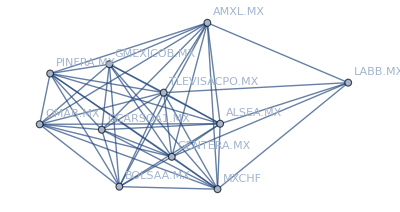

```mathematica
NeighborhoodGraph[graph,4]
```